```mathematica
allGraphs3AtomKeys
```

{13,14,16,22,26}

```mathematica
MakeCord[n_]:=Table[If[k==n,ChromaticPolynomial[allGraphs5[allGraphs5NullAtomKeys[[k]],"graph"],4],0],{k,1,52}]
```

```mathematica
MakeCord[n_,g_]:=Table[If[k==n,ChromaticPolynomial[,0],{k,1,52}]
```

```mathematica
MakeCord[3]
```

{0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
coord=Association[];Table[coord[allGraphs5[allGraphs5NullAtomKeys[[k]],"colofourrealnull"]]=MakeCord[k],{k,1,52}];
```

```mathematica
repCoord = Table[allGraphs5[allGraphs5NullAtomKeys[[k]],"colofourrealnull"]->MakeCord[k],{k,1,52}];
```

```mathematica
{n123,n12x3,n13x2,n1x23,n1x2x3}/.repCoord
```

{n123,n12x3,n13x2,n1x23,n1x2x3}

```mathematica
Table[coord[allGraphs5[k,"colofourrealnull"]]=allGraphs5[k,"colofourrealnull"]/.repCoord,{k,Keys[allGraphs5]}];
```

```mathematica
Values[coord]
```

{{1024,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,256,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},1889,{1024,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-256,0},{1024,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,64,-256,-256},{1024,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-256}}
 |  |  |  |

```mathematica
Map[FactorInteger[First[#]]&,Map[Norm[#]^2&,Values[coord]]//Tally//Sort]//Sort//TableForm
```

2
4 |  |  |  | 
2
8 |  |  |  | 
2
12 |  |  |  | 
2
16 |  |  |  | 
2
20 |  |  |  | 
2
4 | 17
1 |  |  | 
2
4 | 17
2 |  |  | 
2
4 | 17
3 |  |  | 
2
4 | 17
4 |  |  | 
2
4 | 94561
1 |  |  | 
2
6 | 1493
1 |  |  | 
2
6 | 23669
1 |  |  | 
2
6 | 29021
1 |  |  | 
2
8 | 17
1 |  |  | 
2
8 | 17
2 |  |  | 
2
8 | 17
3 |  |  | 
2
8 | 349
1 |  |  | 
2
10 | 1493
1 |  |  | 
2
10 | 1583
1 |  |  | 
2
12 | 17
1 |  |  | 
2
12 | 17
2 |  |  | 
2
12 | 349
1 |  |  | 
2
12 | 487
1 |  |  | 
2
16 | 17
1 |  |  | 
2
6 | 3
1 | 8423
1 |  | 
2
6 | 7
1 | 11
1 |  | 
2
6 | 17
1 | 1493
1 |  | 
2
8 | 3
1 | 43
2 |  | 
2
8 | 7
2 | 11
2 |  | 
2
8 | 13
1 | 521
1 |  | 
2
8 | 17
1 | 349
1 |  | 
2
10 | 7
1 | 11
1 |  | 
2
11 | 7
1 | 113
1 |  | 
2
14 | 7
1 | 11
1 |  | 
2
4 | 5
2 | 11
1 | 19
1 | 
2
6 | 3
2 | 5
1 | 601
1 | 
2
6 | 7
1 | 11
1 | 17
1 | 
2
6 | 7
1 | 11
1 | 17
2 | 
2
8 | 5
2 | 11
1 | 19
1 | 
2
10 | 7
1 | 11
1 | 17
1 | 
2
4 | 5
2 | 11
1 | 17
1 | 19
1

```mathematica
Map[Norm[#]^2&,Values[coord]]//Sort//Tally
```

{{16,1},{256,15},{272,15},{4096,25},{4352,75},{4624,75},{4928,25},{65536,10},{69632,60},{73984,150},{78608,160},{78848,40},{83600,30},{83776,120},{89344,60},{95552,10},{1048576,1},{1114112,10},{1183744,45},{1257728,110},{1261568,10},{1336336,125},{1337600,15},{1340416,70},{1420032,12},{1421200,60},{1424192,150},{1429504,30},{1512976,10},{1514816,60},{1517824,15},{1518848,120},{1528832,5},{1617216,30},{1619968,60},{1620992,10},{1624384,20},{1730880,15},{1733888,30},{1857344,10},{1994752,1}}

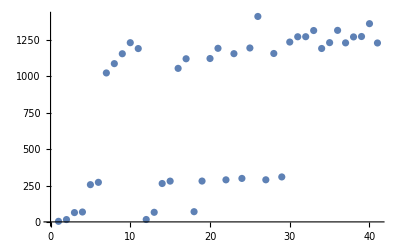

```mathematica
Map[First,(Map[Norm[#]&,Values[coord]]//Tally//Sort)]//ListPlot
```